## Code from and for the well-mixed stochastic CRN simulator

This is the simulator that can pre-process large (many reactions) CRNs for faster simulation, as used in the WalkSATCRN paper.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["CRNSimulator.m"]
Get["CRNSimulatorSSA5.m"]
```

## Running the “Homework Solution 6” CRN

I initially thought that the ColoringCRN can be considered a CRN implementation approximating the Petford & Welsh 1989 randomized algorithm.   In her final report, Pippa investigates the RandomizedCRN, but I think it is the same CRN.   Neither is a good name.  Going forward, I suggest “ConflictColoringCRN” because the essence of this algorithm is directed by coloring conflicts and there is little else going on.  (As we will see below, Petford & Welsh actually had several variants, and this CRN is closest to one of their not-so-good variants.)

```mathematica
ColoringCRN[G_,k_]:=Flatten[Join[
Table[rxn[V[v],V[v,c],1],{v,VertexList[G]},{c,Range[k]}],  (* a vertex without a color will randomly choose a color *)Table[rxn[V[First[e],c]+V[Last[e],c],V[First[e]]+V[Last[e]],1],{e,EdgeList[G]},{c,Range[k]}], (* conflicting edges recolor *)
Table[conc[V[v],1],{v,VertexList[G]}] (* each vertex starts uncolored *)
]]
```

```mathematica
VerifyColoringCRN[G_,k_]:=Module[{rsys,cputime,times,data,finishconcs,results},
rsys=CompiledRxnsysSSA[ColoringCRN[G,k]];
{times,data}=SimulateRxnsysSSA[rsys,Infinity,Output->"State"];
finishconcs=MapThread[conc[#1,#2]&,{SpeciesInRxnsys[rsys],Last[data]}];
results=Cases[finishconcs,conc[V[v_,c_],_?Positive]:>(v->c)];
Sort[First/@results]===Sort[VertexList[G]] &&Length[results]===VertexCount[G]&&
Not[AnyTrue[EdgeList[G],((#[[1]]/.results)===(#[[2]]/.results))&]]
]
```

```mathematica
TimeColoringCRN[G_,k_]:=Module[{rsys,cputime,times,states},
rsys=CompiledRxnsysSSA[ColoringCRN[G,k]];
{cputime,{times,states}}=AbsoluteTiming[SimulateRxnsysSSA[rsys,Infinity,Output->"State"]];
{cputime,Length[times],Last[times]}]
```

It will also be useful to ask Mathematica to call MiniSAT to solve coloring problems.

Given a graph G with N vertices and E edges, we use variables V[v,c] to mean vertex v is colored c.  So for each edge {i,j} we have 
	(!V[i,1] || !V[j,1]) && ... &&  (!V[i,k] || !V[j,k]) 
and then to ensure that each vertex is given exactly 1 color
	(V[i,1] || ... || V[i,k]) && (!V[i,1] || !V[i,2]) && ... && (!V[i,k-1] || !V[i,k])
This is not 3-SAT, but it is K-SAT.

See “Another look at graph coloring via propositional satisfiability” by Allen Van Gelder (2008) for alternative (possibly much better) ways for encoding graph coloring as SAT problems.

```mathematica
ColoringSAT[G_,k_]:=With[{v=VertexList[G],e=EdgeList[G]},
And@@Flatten[Join[
Table[!V[edge[[1]],c]||!V[edge[[2]],c],{c,Range[k]},{edge,e}],
Table[Or@@Table[V[i,c],{c,Range[k]}],{i,v}],
Table[!V[i,c1]||!V[i,c2],{c1,1,k-1},{c2,c1+1,k},{i,v}]
]]]
```

## Reproducing Petford & Welsh’s phase transitions for graph coloring

A surprising thing about the Petford & Welsh paper is that it shows the algorithm consistently and effectively solving 3-coloring problems of up to 1000 vertices.  Below, we will see that on random graphs (generated with iid edges and selected by MiniSAT to be colorable) ColoringCRN has trouble going to even 15-vertex graphs.  Is this because the CRN version of the algorithm is somehow significantly different based on some bias in how random moves are selected, or is this because Petford & Welsh generated super-easy-to-solve graphs?  

Let’s generate graphs their way, and see.  Their method of generating 3-colorable graphs is, given n=n1+n2+n3 and p, to color vertices 1...n1 color 1, vertices n1+1...n1+n2 color 2, and n1+n2+1...n color 3, then to add non-conflicting edges with iid probability p each  (and permute all vertex names if that makes you feel better).  Generalization to k > 3 is straightforward.

```mathematica
PetfordWelshRandomGraph[ns_,p_]:=Module[{m,n=Total[ns],k=Length[ns],i},
m=Table[If[RandomReal[]<Sqrt[p],1,0],n,n]; m=m*Transpose[m]; (* symmetric with prob p off-diagonal*)
For[i=1,i≤k,i++,m[[Total[Take[ns,i-1]]+1;;Total[Take[ns,i]],Total[Take[ns,i-1]]+1;;Total[Take[ns,i]]]]=0]; (* no edges within color class *)
AdjacencyGraph[m]
]
```

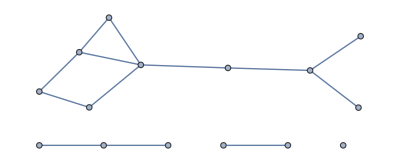

```mathematica
PetfordWelshRandomGraph[{5,5,5},.2]
```

We’ll use TimeColoringCRN to attempt the coloring.  Just to double-check, we’ll also use VerifyColoringCRN, as well as ColoringSAT, to make sure the resulting coloring is valid, and that the generated graph is colorable.   Surprisingly, ColoringCRN can easily solve 30-vertex problems when the number of edges is not too many, but utterly fails when there are many edges.

```mathematica
SatisfiableQ[ColoringSAT[PetfordWelshRandomGraph[{50,50,50},.4]]]
```

True

```mathematica
SatisfiableQ[ColoringSAT[PetfordWelshRandomGraph[{300,300,400},.4]]]
```

True

```mathematica
VerifyColoringCRN[PetfordWelshRandomGraph[{5,5,5},0.5],3]
```

True

```mathematica
VerifyColoringCRN[PetfordWelshRandomGraph[{5,5,5},0.9],3]
```

True

```mathematica
TimeColoringCRN[PetfordWelshRandomGraph[{10,10,10},0.2],3]
```

{0.049576,2,343.427}

```mathematica
TimeColoringCRN[PetfordWelshRandomGraph[{10,10,10},0.5],3]
```

$Aborted

Looking more closely at Petford & Welsh, we see that they consider different ways of randomly choosing colors when recoloring.  Specifically, their algorithm for 3-coloring is a CTMC such that every “bad” vertex has the same propensity for firing, and when a vertex v fires, it chooses (perhaps unchanged) color c with probability
	p(s_1,s_2,s_3; c)
where s_i is the number of neighbors of color i.  “Bad” means that the vertex is in conflict with some neighbor.  They consider a few choices:

	p(s_1,s_2,s_3; c)=1/2(1-s_c/(s_1+s_2+s_3))			This corresponds to randomly choosing a neighbor, and coloring oneself any color other than that neighbor.
	
	p(s_1,s_2,s_3; c) ~ 1/s_c				Normalize over c.  They say this works poorly. [not clear what they mean if s_c=0.  if available, always choose a color with no neighbors?]
	
	p(s_1,s_2,s_3; c) ~ 1/s_c^2				Normalize over c.  They say this works poorly also. [also not clear what they mean if s_c=0.]
	
	p(s_1,s_2,s_3; c) ~ 4^-s_c					Normalize over c.  They say this works surprisingly well, observe linear-in-n time for random graphs of size {n/3,n/3,n/3} and p=0.5.
	
Our CRN doesn’t do any of these exactly.   In our CRN, the reactions that choose and recolor vertex v have total propensity (k-1) b(v) where b(v) is the number of same-colored neighbors.  So unlike P&W, we recolor vertices with more conflicts faster than vertices with fewer conflicts.   However, when we recolor, we always change the color; P&W might choose the current color and stick with it.  But we could imaging including CRN reactions not just for conflicts, but also for each neighbor that is OK -- but these reactions do nothing.  If we also scale every reaction for vertex v (whether it recolors it or not) by 1/d where d is its degree, then the total rate of reactions that change (or don’t change) v is the same for all v.   Thus, our CRN will effectively be choosing a vertex at random, then choosing an edge at random, then choosing a random new color if there was a conflict.   This seems to correspond closely to P&W’s first case, but not quite: P&W allow choosing a vertex that has a conflict and an edge that is not a conflict, yet still flipping the color.  Ignoring such hypothetical changes, the actual ColoringCRN as defined above is equivalent to: choose a vertex in proportion to its degree, choose an edge at random, if the edge is a conflict then recolor with a non-conflicting color.  Still seems similar enough to P&W’s first case that I wouldn’t expect significantly different performance. 

P&W’s fourth case, which they examine extensively because it worked well in their hands, could be described as: 
	choose a vertex with a conflict
	create species “change to 1”, “change to 2”, “change to 3”.
	for each edge to neighbor i colored c, allow reaction “neighbor i” + “change to c” --> “neighbor i”.    
		so probability that “change to c” is still present after time t is e^(-s_c t).
	at time t= ln 4, execute any change that is remaining, and clean up the others.

It would be interesting to design a CRN that explicitly attempts to borrow the principles of P&W’s fourth case, but we won’t do that here.

Instead, we’ll implement P&W#4 as a direct algorithm rather than as a CRN, and try to write fast-to-compile code.

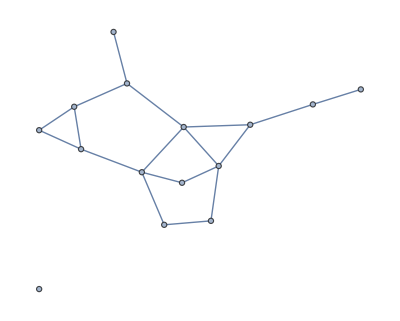

```mathematica
G=PetfordWelshRandomGraph[{5,5,5},.2]
```

```mathematica
PetfordWelshColoring[G_,k_]:=Module[{neighborlists,degree,paddedNL},
neighborlists=AdjacencyList[G,#]&/@VertexList[G];
degree=Max[Length/@neighborlists];
paddedNL=Join[{Length[#]},PadRight[#,degree]]&/@neighborlists; (* Mathematica compiled functions cannot accept ragged list-of-lists *)
PetfordWelshEngine[paddedNL,k]
]
```

```mathematica
PetfordWelshEngine=Compile[{{pnl,_Integer,2},{k,_Integer}}, Module[{n=Length[pnl],d=Length[pnl[[1]]]-1,c,bad,numbad,i,s,j,jj,v,si},
c=Table[1,{n}]; (* initial colors are all 1 *)
bad=Table[1,{n}]; (* does the vertex have a conflict? we assume all vertices have at least one edge. if wrong, this will correct itself. *)
numbad=n;
While[numbad>0 ,
i=RandomInteger[{1,n}];While[bad[[i]]==0,i=Mod[i+1,n,1]];
s=Table[0,{k}];
For[j=1,j≤pnl[[i,1]],j++,s[[c[[pnl[[i,1+j]]]]]]++]; (* count how many neighbors of each color *)
c[[i]]=RandomChoice[4^(-1.0 s)->Range[k]];
For[si=0;j=1,j≤pnl[[i,1]],j++,If[c[[pnl[[i,1+j]]]]==c[[i]],si++]]; (* count number of conflicts *)
If[si==0,bad[[i]]=0;numbad--];
For[j=1,j≤pnl[[i,1]],j++, (* now update badness state of neighbors *)
v=pnl[[i,1+j]];
If[bad[[v]]==1,numbad--];bad[[v]]=0;
For[si=0;jj=1,jj≤pnl[[v,1]],jj++,If[c[[pnl[[v,1+jj]]]]==c[[v]],si++]];
If[si>0,bad[[v]]=1;numbad++]
]
];
c]]
```

CompiledFunction[…]

```mathematica
c=PetfordWelshColoring[G,3]
```

{2,1,3,1,1,1,3,1,3,2,3,1,3,2,1}

```mathematica
VerifyColoring[G_,k_,c_]:=Not[AnyTrue[EdgeList[G],(c[[#[[1]]]]==c[[#[[2]]]])&]]&&Min[c]≥1&&Max[c]≤k
```

```mathematica
VerifyColoring[G,3,c=PetfordWelshColoring[G,3]]
```

True

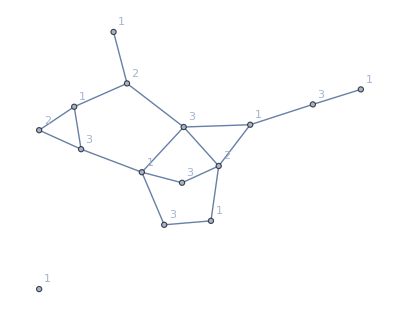

```mathematica
Graph[G,VertexLabels->Table[i->c[[i]],{i,VertexList[G]}]]
```

Now let’s see whether our P&W#4 algorithm runs efficiently enough to solve large coloring problems -- e.g. up to 1000 vertices -- as the paper reports.   No problem.  So then, we should be able to roughly reproduce the figures from that paper.

```mathematica
n3=500;
G=PetfordWelshRandomGraph[{n3,n3,n3},.2];
c=PetfordWelshColoring[G,3];
VerifyColoring[G,3,c]
```

True

```mathematica
PWtime[n_,p_]:=Module[{G,c,t,n3=Round[n/3]},
G=PetfordWelshRandomGraph[{n3,n3,n3},p];(*Print["f=",N[EdgeCount[G]/VertexCount[G]]];*)
{t,c}=Timing[PetfordWelshColoring[G,3]];
If[Not[VerifyColoring[G,3,c]],Print["Miscolored"]];
t]
```

```mathematica
Fig1a=Table[(Print[#];#)&@{n,Mean[Table[PWtime[n,0.5],100]]},{n,{60,120,180,240,300}}];
```

```mathematica
Fig1b=Table[(Print[#];#)&@{n,Mean[Table[PWtime[n,0.9],100]]},{n,{60,120,180,240,300}}];
```

```mathematica
Fig1c=Table[(Print[#];#)&@{n,Mean[Table[PWtime[n,0.3],100]]},{n,{60,120,180,240,300}}];
```

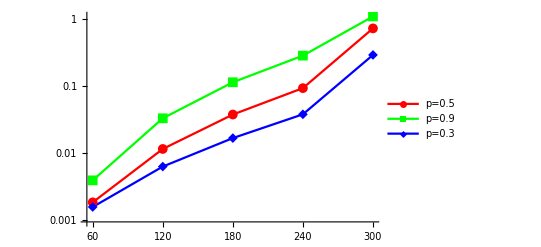

```mathematica
ListLogPlot[{Fig1a,Fig1b,Fig1c},PlotRange->All,PlotStyle->{Red,Green,Blue},Joined->True,PlotMarkers->{Automatic,10},PlotLegends->{"p=0.5","p=0.9","p=0.3"}]
```

```mathematica
Fig2=Table[(Print[#];#)&@{n,Mean[Table[PWtime[n,0.5],10]]},{n,Range[60,900,60]}];
```

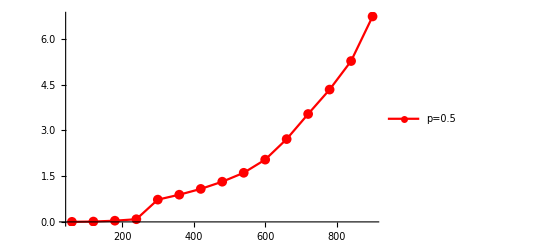
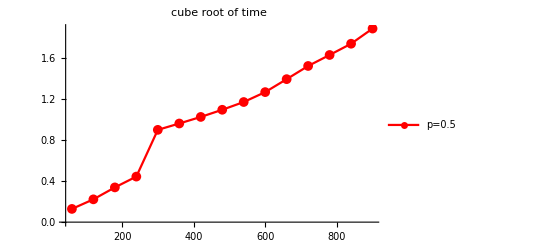
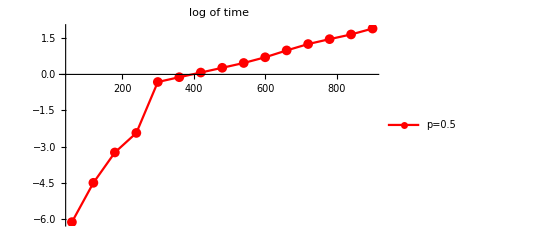

```mathematica
{ ListPlot[Fig2,PlotRange->All,PlotStyle->{Red},Joined->True,PlotMarkers->{Automatic,10},PlotLegends->{"p=0.5"}],
ListPlot[{#[[1]],(#[[2]])^(1/3)}&/@Fig2,PlotRange->All,PlotStyle->{Red},Joined->True,PlotMarkers->{Automatic,10},PlotLegends->{"p=0.5"},PlotLabel->"cube root of time"],
ListPlot[{#[[1]],Log[#[[2]]]}&/@Fig2,PlotRange->All,PlotStyle->{Red},Joined->True,PlotMarkers->{Automatic,10},PlotLegends->{"p=0.5"},PlotLabel->"log of time"] }
```

This doesn’t look linear like P&W’s figure 2.  An obvious difference: P&W are plotting the number of vertex updates, while we are measuring CPU time.  Thus, our algorithm’s implementation and efficiency play a role, not just the mathematical Markov Chain.    Each update of our implementation takes O(d^2) time where d is the average vertex degree of the graph, and for these graphs d = O(n).  So if the number of steps is O(n), our algorithm would take real time O(n^3).   Other than the obvious jump around n=300 that probably (?) has to do with memory cache utilization, this is not entirely implausible. 

Still, going up to 900 vertices and being fast enough to time 100 trials is good news.  As a reference point, are we anywhere close to as fast as MiniSAT?

```mathematica
PWtimeSAT[n_,p_]:=Module[{G,v,t,n3=Round[n/3],sat},
G=PetfordWelshRandomGraph[{n3,n3,n3},p];sat=ColoringSAT[G,3];
{t,v}=Timing[SatisfiableQ[sat]];
t]
```

```mathematica
Fig2sat=Table[(Print[#];#)&@{n,Mean[Table[PWtimeSAT[n,0.5],10]]},{n,Range[60,900,60]}];
```

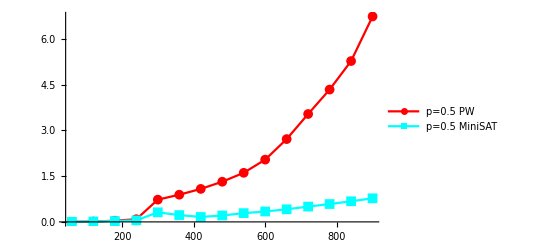

```mathematica
ListPlot[{Fig2,Fig2sat},PlotRange->All,PlotStyle->{Red,Cyan},Joined->True,PlotMarkers->{Automatic,10},PlotLegends->{"p=0.5 PW","p=0.5 MiniSAT"}]
```

Comparing with MiniSAT suggests that the PW method of creating graphs does not generally create hard ones -- and further, the n=300 point may actually be where the p=0.5 parameter yields hard problems, rather than being a cache memory issue.

```mathematica
Fig4=Table[(Print[#];#)&@{n,Mean[Table[PWtime[n,0.1],100]]},{n,Range[10,120]}];
```

```mathematica
Fig4sat=Table[(Print[#];#)&@{n,Mean[Table[PWtimeSAT[n,0.1],100]]},{n,Range[10,120]}];
```

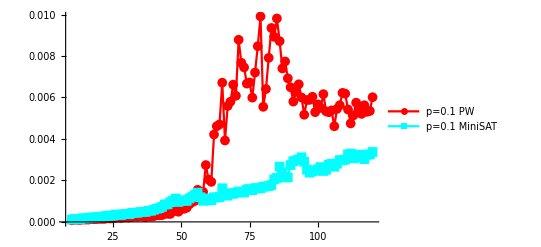

```mathematica
ListPlot[{Fig4,Fig4sat},PlotRange->All,PlotStyle->{Red,Cyan},Joined->True,PlotMarkers->{Automatic,10},PlotLegends->{"p=0.1 PW","p=0.1 MiniSAT"}]
```

Interestingly, it seems that the “critical values” observed by P&W were critically difficult for their algorithm, but did not represent generally hard problems (at least from MiniSAT’s perspective).

```mathematica
Fig4alt=Table[(Print[#];#)&@{p,Mean[Table[PWtime[200,p],100]]},{p,Range[0.02,0.98,0.02]}];
```

```mathematica
Fig4altsat=Table[(Print[#];#)&@{p,Mean[Table[PWtimeSAT[200,p],100]]},{p,Range[0.02,0.98,.02]}];
```

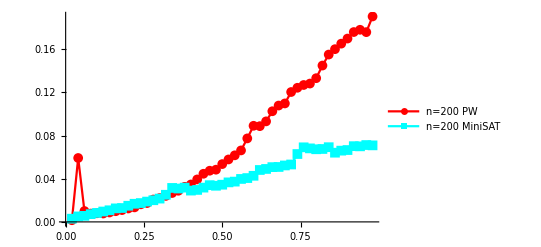

```mathematica
ListPlot[{Fig4alt,Fig4altsat},PlotRange->All,PlotStyle->{Red,Cyan},Joined->True,PlotMarkers->{Automatic,10},PlotLegends->{"n=200 PW","n=200 MiniSAT"}]
```

```mathematica
Fig4altX=Table[(Print[#];#)&@{p,Mean[Table[PWtime[200,p],100]]},{p,Range[0.005,0.1,0.001]}];
```

```mathematica
Fig4altsatX=Table[(Print[#];#)&@{p,Mean[Table[PWtimeSAT[200,p],100]]},{p,Range[0.005,0.1,0.001]}];
```

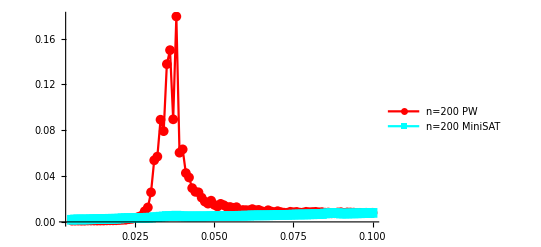

```mathematica
ListPlot[{Fig4altX,Fig4altsatX},PlotRange->All,PlotStyle->{Red,Cyan},Joined->True,PlotMarkers->{Automatic,10},PlotLegends->{"n=200 PW","n=200 MiniSAT"}]
```

Zooming in on the P&W generated random graphs, we sure see that they are hard for P&W’s algorithm, but not for MiniSAT.  For n=200 and p=0.0375, the graph will have about m=(3 ×66^2 ×0.0375)= 490 edges, so m/n=2.45.  This seems to be about the threshold (maybe 2.4) for 3-colorability of random graphs.  Yet for more edges, these graphs are easy.

Finally, let’s examine random unstructured graphs selected for being solvable.  P&W is not good at these, even though it handles well its own graphs with the same edge/vertex ratios!  So they really are harder than the P&W-generated graphs.  Surprising!

```mathematica
PWtimerand[n_,f_]:=Module[{G,c,t,sat},
G=RandomGraph[{n,Round[f n]}];sat=ColoringSAT[G,3];
While[Not[SatisfiableQ[sat]],G=RandomGraph[{n,Round[f n]}];sat=ColoringSAT[G,3]];
{t,c}=Timing[PetfordWelshColoring[G,3]];
If[Not[VerifyColoring[G,3,c]],Print["Miscolored"]];
t]
```

```mathematica
PWtimeSATrand[n_,f_]:=Module[{G,v,t,sat},
G=RandomGraph[{n,Round[f n]}];sat=ColoringSAT[G,3];
While[Not[SatisfiableQ[sat]],G=RandomGraph[{n,Round[f n]}];sat=ColoringSAT[G,3]];
{t,v}=Timing[SatisfiableQ[sat]];
t]
```

```mathematica
FigAltSAT=Table[(Print[#];#)&@{f,Mean[Table[PWtimeSATrand[200,f],10]]},{f,Range[2.2,2.45,0.05]}];
```

```mathematica
(* too slow to run more than just 10 samples each! *)
FigAlt=Table[(Print[#];#)&@{f,Mean[Table[PWtimerand[200,f],10]]},{f,Range[2.2,2.45,0.05]}];
```

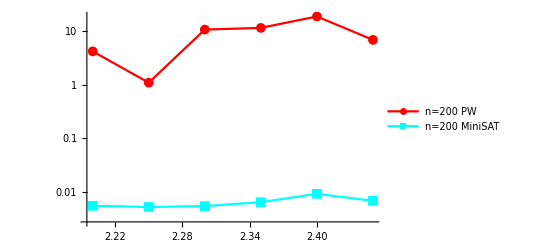

```mathematica
ListLogPlot[{FigAlt,FigAltSAT},PlotRange->All,PlotStyle->{Red,Cyan},Joined->True,PlotMarkers->{Automatic,10},PlotLegends->{"n=200 PW","n=200 MiniSAT"}]
```

Plotting P&W-generated graphs vs the actual f=m/n (for P&W algorithm only), we confirm that this way of generating graphs really results in easier graphs for the same ratio.  P&W seems to be on average about 100x faster, while MiniSAT is maybe only 5x faster (solving P&W-generated random colorable graphs, vs solving random n-m graphs selected for being colorable).

```mathematica
PWtimeF[n_,p_]:=Module[{G,c,t,n3=Round[n/3],f},
G=PetfordWelshRandomGraph[{n3,n3,n3},p];f=N[EdgeCount[G]/VertexCount[G]];
{t,c}=Timing[PetfordWelshColoring[G,3]];
If[Not[VerifyColoring[G,3,c]],Print["Miscolored"]];
{f,t}]
```

```mathematica
PWtimeSATF[n_,p_]:=Module[{G,v,t,n3=Round[n/3],sat,f},
G=PetfordWelshRandomGraph[{n3,n3,n3},p];sat=ColoringSAT[G,3]; f=N[EdgeCount[G]/VertexCount[G]];
{t,v}=Timing[SatisfiableQ[sat]];
{f,t}]
```

```mathematica
(* double-check the same edge/vertex ratio generated via P&W's method.  f=m/n=(3*66^2*p)/n so p=f*n/3/66^2... but here f has std ~ 0.2. *)
(* So tally by actual f rather than parameter dictating mean f. *)
FigAltX=Table[(If[RandomReal[]<0.01,Print[#]];#)&@PWtimeF[200,f 200/(3 66^2)],{f,Range[2.2,2.45,0.01/100]}];
```

```mathematica
FigAltSATX=Table[(If[RandomReal[]<0.01,Print[#]];#)&@PWtimeSATF[200,f 200/(3 66^2)],{f,Range[2.2,2.45,0.01/100]}];
```

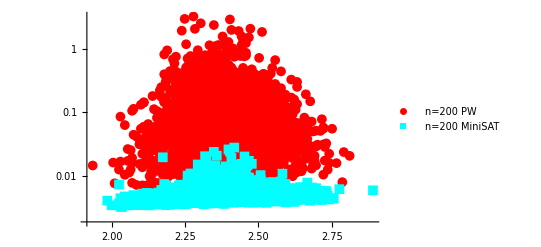

```mathematica
ListLogPlot[{FigAltX,FigAltSATX},PlotRange->All,PlotStyle->{Red,Cyan},Joined->False,PlotMarkers->{Automatic,10},PlotLegends->{"n=200 PW","n=200 MiniSAT"}]
```

It is also fair to comment that the PW algorithm is sometimes decent, only say 10x worse than MiniSAT, which is pretty good!  But on the hardest problems, it can be 1000x slower...